### Preprocess data

Import raw data

```mathematica
rawdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\New data set\\data\\data (not normalized).xlsx"];
```

Synthesize missing values:

```mathematica
data1=Table[Values[Transpose[Normal[SynthesizeMissingValues[Normal[rawdata[All,{2,3,i}]],Method-><|"LearningMethod"->"KernelDensityEstimation", "EvaluationStrategy"->"ModeFinding"|>,PerformanceGoal->"Quality"]]]⟦3⟧],{i,4,41}];
```

```mathematica
Export["data (synthesized missing values).csv",Transpose[data1]];
```

```mathematica
rawdata2=Transpose[data1];
rawdata2=Transpose[Table[N[Standardize[rawdata2[[All,k]]]],{k,1,38}]];
Export["data standardized.csv",rawdata2]
```

data standardized.csv

## Classification

Import data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\New data set\\data\\data.xlsx"];
data=Values[Normal[importdata]]⟦All,2;;42⟧;
labels=Import["D:\\Google Drive\\Rich Internship 2020\\New data set\\data\\data.xlsx"][[1]][[1]];
```

#### column labels

```mathematica
Table[{i,labels⟦i⟧},{i,1,42}]//TableForm
```

1 | patient_id
2 | age
3 | gender
4 | white blood cell
5 | Eosinophil
6 | lactate dehydrogenase
7 | C-reactive protein
8 | Monocyte
9 | Alanine transaminase
10 | Aspartate transaminase
11 | Glomerular filtration rate
12 | Partial Pressure Of Oxygen
13 | Hemoglobin
14 | red blood cell
15 | Hematocrit
16 | Platelet
17 | Albumin
18 | Total bilirubin
19 | Potassium
20 | Sodium
21 | Chlorine
22 | Anion gap
23 | PH
24 | PaCO2
25 | Blood oxygen saturation
26 | Respiratory index
27 | B-type Natriuretic Peptide
28 | Myoglobin
29 | Troponin I
30 | Urine specific gravity
31 | Urine leukocyte
32 | Urinary Erythrocytes
33 | Urea
34 | Uric acid
35 | AST-ALT ratio
36 | Total protein
37 | Globulin
38 | Plasma prothrombin time
39 | Thrombin time
40 | Plasma fibrinogen
41 | Creatine kinase isoenzyme
42 | Severity

## severity classification model

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data,285];
```

Split data into 80% training and 20% test

```mathematica
trainingset=rs⟦1;;0.80*285⟧;
testset=rs⟦0.80*285+1;;285⟧;
```

```mathematica
c=Classify[trainingset->41,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

### deployed model

```mathematica
SeedRandom[321];
rs=RandomSample[data,285];
```

```mathematica
trainingset=rs⟦1;;285⟧;
```

```mathematica
c=Classify[trainingset->41,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
Information[c]
```

Classifier information
Data type | Mixed (number: 40)
Classes | ,,mildmoderatesevere
Accuracy | (85.23.1) %
Method | NeuralNetwork
Single evaluation time | 3. ms/example
Batch evaluation speed | 60.6 examples/ms
Loss | 0.718 ± 0.16
Model memory | 535. kB
Training examples used | 285 examples
Training time | 13. s
 |

#### severity functions based on age

```mathematica
f[age_]:=Values[c[{age,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦1⟧;
```

```mathematica
g[age_]:=Values[c[{age,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

```mathematica
h[age_]:=Values[c[{age,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦3⟧;
```

#### Plots

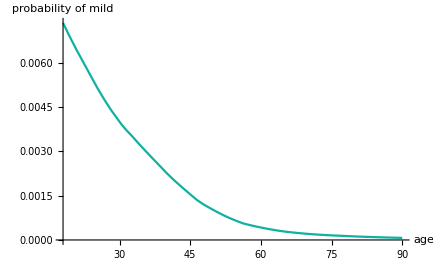

```mathematica
Plot[f[age],{age,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->RGBColor[0.0575287, 0.697632, 0.634101],AxesLabel->{"age","probability of mild"}]
```

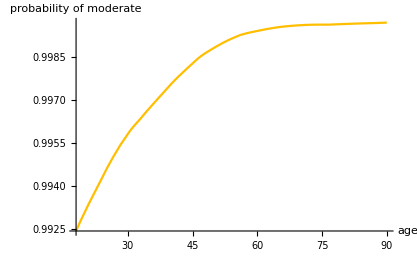

```mathematica
Plot[g[age],{age,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->RGBColor[1, 0.75, 0],AxesLabel->{"age","probability of moderate"}]
```

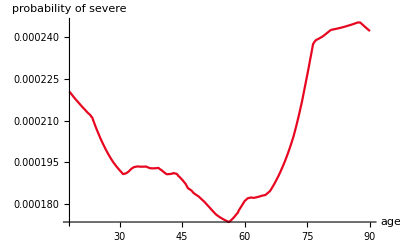

```mathematica
Plot[h[age],{age,Min[data[[All,1]]],Max[data[[All,1]]]},AxesLabel->{"age","probability of severe"},PlotStyle->RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]]
```

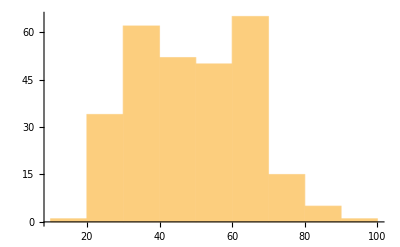

```mathematica
Histogram[data[[All,1]]]
```

### accuracy metrics

#### Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->41]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.894737

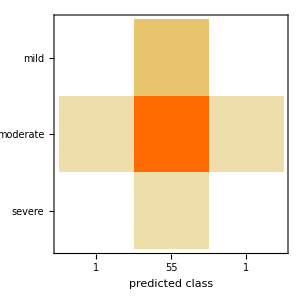

```mathematica
cm["ConfusionMatrixPlot"]
```

## Asymptomatic classification model

Import data

```mathematica
importdata=SemanticImport["D:\\Google Drive\\Rich Internship 2020\\New data set\\data\\data2.xlsx"];
data=Values[Normal[importdata]]⟦All,2;;42⟧;
labels=Import["D:\\Google Drive\\Rich Internship 2020\\New data set\\data\\data2.xlsx"][[1]][[1]];
```

```mathematica
SeedRandom[321];
rs=RandomSample[data,285];
```

```mathematica
trainingset=rs⟦1;;285⟧;
```

```mathematica
c=Classify[trainingset->41,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

### probability of being asymptomatic as a function of age

#### probability function

```mathematica
k[age_]:=Values[c[{age,Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

#### plots

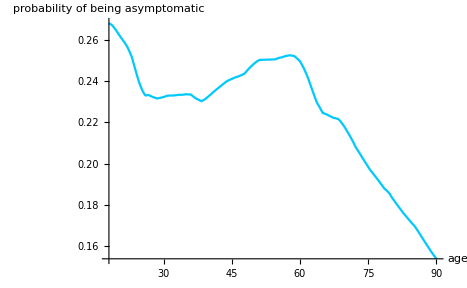

```mathematica
Plot[k[age],{age,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->RGBColor[0., 0.79, 1.],AxesLabel->{"age","probability of being asymptomatic"}]
```

### probability of being asymptomatic as a function of age given gender

#### probability functions

```mathematica
m[age_]:=Values[c[{age,"male",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

```mathematica
female[age_]:=Values[c[{age,"female",Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[],Missing[]},"Probabilities"]]⟦2⟧;
```

#### plots

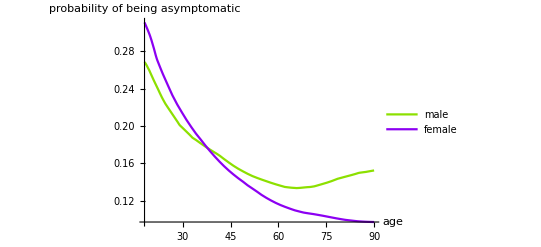

```mathematica
Plot[{m[age],female[age]},{age,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->{RGBColor[0.55, 0.88, 0],RGBColor[0.55, 0, 0.9500000000000001]},AxesLabel->{"age","probability of being asymptomatic"},PlotLegends->{"male","female"}]
```

### accuracy metrics

#### asymptomatic classification model

randomize data for training/test split

```mathematica
SeedRandom[123];
rs=RandomSample[data,285];
```

Split data into 80% training and 20% test

```mathematica
trainingset=rs⟦1;;0.80*285⟧;
testset=rs⟦0.80*285+1;;285⟧;
```

```mathematica
c=Classify[trainingset->41,Method->"NeuralNetwork",PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

#### Accuracy and Confusion Matrix

```mathematica
cm=ClassifierMeasurements[c,testset->41]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.842105

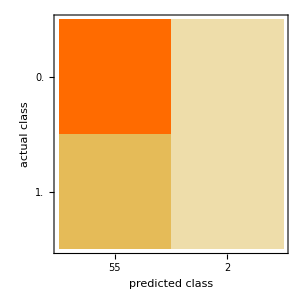

```mathematica
cm["ConfusionMatrixPlot"]
```